```mathematica
Quit[]
```

```mathematica
NotebookEvaluate[EvaluationNotebook[],EvaluationElements->"InitializationCell"];
```

```mathematica
SetDirectory@NotebookDirectory[];
Off[Part::partd,Part::pspec1,Message::name];
```

```mathematica
Clear["Global`*"];
```

## Pre - load

```mathematica
SetDirectory[NotebookDirectory[]];
NormalVector=Normalize@Cross[#⟦2⟧-#⟦1⟧,#⟦3⟧-#⟦1⟧]&;
NodesElements={MeshCoordinates@#, Reverse/@MeshCells[#,2]⟦All,1⟧}&;
Nodes=<||>;
Elements=<||>;
Triangles=<||>;
ModelHash[name_String]:=Hash@Triangles@name;
ModelDir[name_String]:=FileNameJoin@{"Model",name};
ModelPath[name_String]:=FileNameJoin@{ModelDir@name,ToString@ModelHash@name};
ExportModelCSV[name_String,nodes_,elements_]:=
Export[ModelPath@name<>".csv",StringJoin@@Riffle[Join[{ToString@Length@nodes<>","<>ToString@Length@elements,ExportString[nodes,"CSV"]},Flatten[{ToString@Length@#,ExportString[#,"CSV"]}&/@((Reverse/@#)&/@elements),1]],"\n"],"Text"];
ImportModelSTL[name_String]:=Module[{model,nodes,elements},
model=ConnectedMeshComponents@Import@FileNameJoin@{ModelDir@name,name<>".stl"};
{nodes,elements}=(NodesElements/@model)ᵀ;
elements+=Prepend[Accumulate@Most[Length/@nodes],0];
nodes=Join@@nodes;
Nodes[name]=nodes;
Elements[name]=elements;
Triangles[name]=(nodes⟦#⟧&/@(Join@@elements)⟦All,1;;3⟧);
ExportModelCSV[name,nodes,elements];
Table[Show[model,HighlightMesh[model⟦i⟧,Style[1,Red]],ImageSize->30],{i,Length@model}]
];
EqualRange[{x0_,x1_,xn_Integer}]:=If[xn>0,Subdivide[x0,x1,xn],{(x0+x1)/2}];
EqualRange[{x0_,x1_,xn_Integer},{y0_,y1_,yn_Integer}]:=Table[{x,y},{x,EqualRange@{x0,x1,xn}},{y,EqualRange@{y0,y1,yn}}];
EqualRange[{x0_,x1_,xn_Integer},{y0_,y1_,yn_Integer},{z0_,z1_,zn_Integer}]:=Table[{x,y,z},{x,EqualRange@{x0,x1,xn}},{y,EqualRange@{y0,y1,yn}},{z,EqualRange@{z0,z1,zn}}];
EqualRangeInterpolation[x_,{x0_,x1_,xn_Integer}]:=Module[
{nx,dx,ix,coe,idx},
nx=xn+1;
dx=If[xn>0,(x-x0)/(x1-x0)*xn,0];
ix=Floor@dx;
dx-=ix;
coe={1-dx,dx};
idx=1+{ix,1+ix};
With[{c=coe,i=idx},c.#⟦i⟧&]
];
EqualRangeInterpolation[{x_,y_},{x0_,x1_,xn_Integer},{y0_,y1_,yn_Integer}]:=Module[
{nx,ny,dx,dy,ix,iy,coe,idx},
{nx,ny}={xn,yn}+1;
dx=If[xn>0,(x-x0)/(x1-x0)*xn,0];
dy=If[yn>0,(y-y0)/(y1-y0)*yn,0];
{ix,iy}=Floor/@{dx,dy};
{dx,dy}-={ix,iy};
coe={(1-dx)(1-dy),(1-dx)dy,dx(1-dy),dx dy};
idx=1+{iy+ix ny,1+iy+ix ny,iy+(1+ix)ny,1+iy+(1+ix)ny};
With[{c=coe,i=idx},c.#⟦i⟧&]
];
EqualRangeInterpolation[{x_,y_,z_},{x0_,x1_,xn_Integer},{y0_,y1_,yn_Integer},{z0_,z1_,zn_Integer}]:=Module[
{nx,ny,nz,dx,dy,dz,ix,iy,iz,coe,idx},
{nx,ny,nz}={xn,yn,zn}+1;
dx=If[xn>0,(x-x0)/(x1-x0)*xn,0];
dy=If[yn>0,(y-y0)/(y1-y0)*yn,0];
dz=If[zn>0,(z-z0)/(z1-z0)*zn,0];
{ix,iy,iz}=Floor/@{dx,dy,dz};
{dx,dy,dz}-={ix,iy,iz};
coe={(1-dx) (1-dy) (1-dz),(1-dx) (1-dy) dz,(1-dx) dy (1-dz),(1-dx) dy dz,dx (1-dy) (1-dz),dx (1-dy) dz,dx dy (1-dz),dx dy dz};
idx=1+{iz+iy nz+ix ny nz,1+iz+iy nz+ix ny nz,iz+(1+iy) nz+ix ny nz,1+iz+(1+iy) nz+ix ny nz,iz+iy nz+(1+ix) ny nz,1+iz+iy nz+(1+ix) ny nz,iz+(1+iy) nz+(1+ix) ny nz,1+iz+(1+iy) nz+(1+ix) ny nz};
With[{c=coe,i=idx},c.#⟦i⟧&]
];
```

### LuaLink

```mathematica
If[ValueQ@BemWorld,BemDelWorld/@Values[BemWorld]];
```

```mathematica
BemWorld=<||>;
```

```mathematica
Install[(*"cmd /k "<>*)FileNameJoin@{NotebookDirectory[],"Lua","luajit.exe "}<>FileNameJoin@{NotebookDirectory[],"Lua","LuaLink.lua"}];
LuaFunctionCast[name_String]:=Lua["function(...)return "<>name<>"(...)end"];
```

```mathematica
Lua["ffi = require('ffi')
local file = io.open([["<>FileNameJoin@{NotebookDirectory[],"BEM","BEM.lua.h"}<>"]])
bem = ffi.load('BEM')
ffi.cdef(file:read('*all'))
file:close()"]
```

```mathematica
BemNewWorld=LuaFunctionCast["bem.new_world"];
BemLoadCsv=LuaFunctionCast["bem.load_csv"];
BemSolve=LuaFunctionCast["bem.solve"];
BemRegion=LuaFunctionCast["bem.region"];
BemRegionSlow=LuaFunctionCast["bem.region_slow"];
BemPoint=LuaFunctionCast["bem.point"];
BemPointSlow=LuaFunctionCast["bem.point_slow"];
BemDelWorld=LuaFunctionCast["bem.del_world"];
BemGetWorld[name_String]:=Module[{wr},
wr=BemWorld@ModelHash@name;
If[Head@wr=!=LuaObject,
BemWorld@ModelHash@name=wr=BemNewWorld[ModelPath@name<>".data",0.0001,64,6,6,1,1000];
BemLoadCsv[wr,ModelPath@name<>".csv",44];
];
wr
];
```

#### Uninstall

```mathematica
Uninstall@Last@Links["*LuaLink.lua*"];
LinkClose/@Links["*LuaLink.lua*"];
```

### MATLink

```mathematica
Needs@"MATLink`";
(*SetOptions[MATLink,"Force32BitEngine"->True]*)
OpenMATLAB[]
```

n$::shdw: Symbol n$ appears in multiple contexts {MATLink`Private`,Global`}; definitions in context MATLink`Private` may shadow or be shadowed by other definitions.

```mathematica
permute=MFunction["permute"];
MEvaluate["cd '"<>FileNameJoin@{NotebookDirectory[],"MATLAB'"}];
MPotential=MFunction["Potential","OutputArguments"->4];
MChargeBasis=MFunction["ChargeBasis"];
MPotentialBasis=MFunction["PotentialBasis"];
```

#### Install

copy MATLink folder to $UserBaseDirectory/Applications
add C:\Program Files\MATLAB\R2015b\bin\win64\libmx.dll to PATH

```mathematica
SystemOpen@$UserBaseDirectory;
```

### Fit

```mathematica
FindFitPlot[data_List,arg:{expr_,cons_}|expr_,pars_,x_:Global`x,plot_Symbol:True]:=Module[{fits,func,xmin,xmax},
fits=FindFit[data,arg,pars,x];
func=expr/.fits;
{xmin,xmax}={Min[#],Max[#]}&@Transpose[data][[1]];
If[plot,
Print[Show[ListLinePlot[data,PlotStyle->Red,PlotMarkers->Automatic],Plot[func,{x,xmin,xmax},PlotStyle->Blue]]]];
{fits,expr/.fits}
];

FitPlot[data_List,expr_,x_:Global`x,plot_Symbol:True]:=Module[{func,xmin,xmax},
func=Fit[data,expr,x];
{xmin,xmax}={Min[#],Max[#]}&@Transpose[data][[1]];
If[plot,
Print[Show[ListLinePlot[data,PlotStyle->Red,PlotMarkers->Automatic],Plot[func,{x,xmin,xmax},PlotStyle->Blue]]]];
func
];
```

## Calculate Method

```mathematica
Options[ChargeBasis]={Method->MATLAB};
ChargeBasis[name_String,opts:OptionsPattern[]]:=Module[
{file,func=OptionValue[Method],charges},
file=ModelPath@name<>"-"<>ToString@func<>".mat";
If[FileExistsQ[file],
charges=Import[file]⟦1⟧,
charges=ChargeBasisMethod[func][name];
Export[file,charges]
];
charges
];
ChargeBasisMethod[MATLAB][name_String]:=(MChargeBasis[FileNameJoin@{"..",ModelPath@name}]ᵀ);
ChargeBasisMethod[BEM][name_String]:= Module[
{wr,data,pos,n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum},
wr=BemGetWorld@name;
BemSolve[wr];
data=Import[ModelPath@name<>".data","Byte"];
pos=Prepend[Flatten@Position[data,10,1,7],0];
{n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum}=Read[StringToStream@FromCharacterCode@data⟦#⟧,Number]&/@(Span@@(#+{1,-1})&/@Partition[pos,2,1]);
4π Partition[ImportString[FromCharacterCode@data⟦Last@pos+1;;-1⟧,"Real64"],n]
];
ChargeBasisMethod[CHIBE][name_String]:=Module[
{elements,charges,values},
SetDirectory@"CHIBE";
Export["nodes.csv",Nodes@name];
elements=Elements@name;
charges=Table[
values=Join@@Table[Join[#,{1,KroneckerDelta[k,i]}]&/@elements⟦i⟧,{i,Length@elements}];
Export["elements.csv",values];
Run[FileNameJoin@{"..","Lua","luajit"}<>" preCHIBE.lua "<>name];
Run["3D_Potential_CHBIE_FMM_64"];
values=Rest/@Import["output.dat","Table"]⟦3;;-1⟧;
values⟦All,2⟧
,{k,Length@elements}];
SetDirectory@"..";
charges
];

Options[PotentialBasis]={Method->MATLAB};
PotentialBasis[name_String,{x0_,x1_,xn_Integer},{y0_,y1_,yn_Integer},{z0_,z1_,zn_Integer},opts:OptionsPattern[]]:=Module[
{file,func=OptionValue[Method],potential},
file=ModelPath@name<>"-"<>ToString@Hash@{{x0,x1,xn},{y0,y1,yn},{z0,z1,zn}}<>"-"<>ToString@func<>".mat";
If[FileExistsQ[file],
potential=Import[file],
potential=PotentialBasisMethod[func][name,{x0,x1,xn},{y0,y1,yn},{z0,z1,zn}];
Export[file,potential]
];
potential
];
PotentialBasisMethod[MATLAB][name_String,{x0_,x1_,xn_Integer},{y0_,y1_,yn_Integer},{z0_,z1_,zn_Integer}]:=Module[
{charges,triangles,points},
(*charges=ChargeBasis[name,Method->MATLAB];
triangles=permute[Triangles@name,{2,3,1}];
points=Flatten[EqualRange[{x0,x1,xn},{y0,y1,yn},{z0,z1,zn}],2];
Re@MPotential[triangles,#.charges ,points]&/@IdentityMatrix@Length@Elements@name*)
If[Length@Dimensions@#==2,{#},(#ᵀ&/@#)ᵀ]&@Re@MPotentialBasis[FileNameJoin@{"..",ModelPath@name},{x0,x1,xn},{y0,y1,yn},{z0,z1,zn}]
];
PotentialBasisMethod[BEM][name_String,{x0_,x1_,xn_Integer},{y0_,y1_,yn_Integer},{z0_,z1_,zn_Integer}]:=Module[
{wr,data,pos,n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum,xmin,xmax,nx,ymin,ymax,ny,zmin,zmax,nz},
wr=BemGetWorld@name;
BemSolve[wr];
BemRegion[wr,x0,x1,xn,y0,y1,yn,z0,z1,zn];
data=Import[ModelPath@name<>".datacalc","Byte"];
pos=Prepend[Flatten@Position[data,10,1,16],0];
{n,amountOfElectrodes,tol,maxit,numMom,numLev,checksum,xmin,xmax,nx,ymin,ymax,ny,zmin,zmax,nz}=Read[StringToStream@FromCharacterCode@data⟦#⟧,Number]&/@(Span@@(#+{1,-1})&/@Partition[pos,2,1]);
({1,-1,-1,-1}(Partition[#,nx*ny*nz]&/@Partition[ImportString[FromCharacterCode@data⟦Last@pos+1;;-1⟧,"Real64"],nx*ny*nz*amountOfElectrodes]))ᵀ
];
PotentialBasisMethod[BEMSlow][name_String,{x0_,x1_,xn_Integer},{y0_,y1_,yn_Integer},{z0_,z1_,zn_Integer}]:=Block[{BemRegion=BemRegionSlow},PotentialBasisMethod[BEM][name,{x0,x1,xn},{y0,y1,yn},{z0,z1,zn}]];
```

## sphere

```mathematica
ImportModelSTL@"sphere"
```

{-Graphics3D-}

```mathematica
AbsoluteTiming[cb=ChargeBasis["sphere"];]
```

{0.0367454,Null}

```mathematica
AbsoluteTiming[pb=PotentialBasis["sphere",{-2,2,40},{-2,2,40},{0,0,0}];]
```

{0.0229225,Null}

```mathematica
pb//Dimensions
```

{1,4,1681}

```mathematica
grid=N@Flatten[EqualRange[{-2,2,40},{-2,2,40}],1];
```

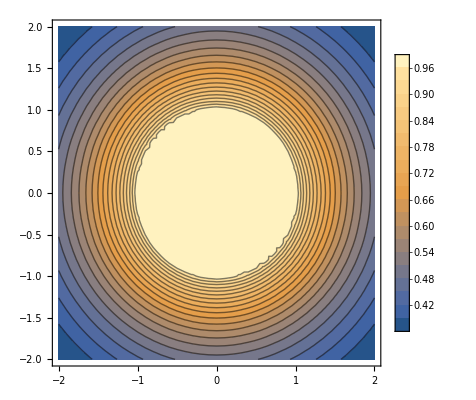

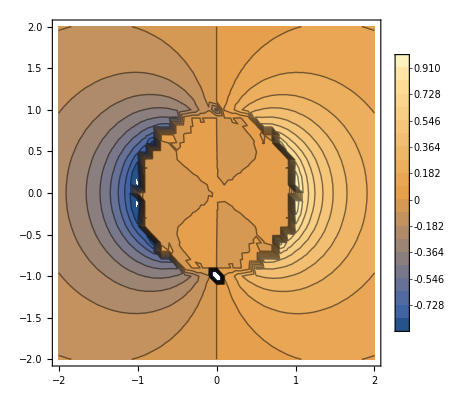

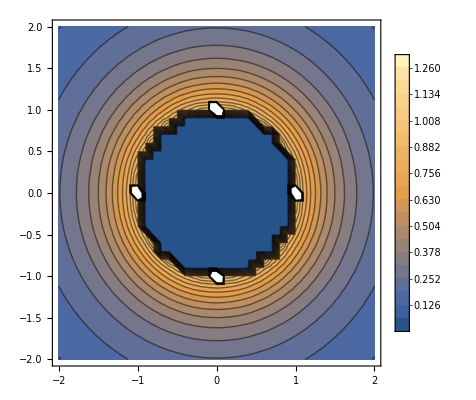

```mathematica
{pot,fx,fy,fz}={1}.pb;
ListContourPlot[Flatten/@({grid,pot}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({grid,fx}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({grid,√(fx^2+fy^2+fz^2)}ᵀ),Contours->20,PlotLegends->Automatic]
```

```mathematica
grid={{-2,2,40},{-2,2,40},{-2,2,40}};
AbsoluteTiming[pb=PotentialBasis["sphere",Sequence@@grid];]
{pot,fx,fy,fz}={1}.pb;
```

{0.0310296,Null}

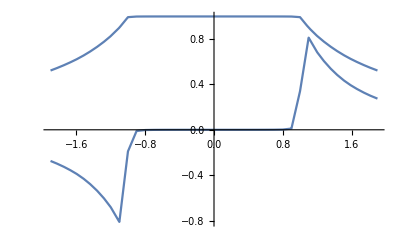

```mathematica
Plot[EqualRangeInterpolation[{x,0,0},Sequence@@grid]/@{pot,fx},{x,-1.9,1.9}]
```

## 4rod

```mathematica
ImportModelSTL@"4rod"
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
AbsoluteTiming[cb=ChargeBasis["4rod"];]
```

{0.0575482,Null}

```mathematica
AbsoluteTiming[pb=PotentialBasis["4rod",{-0.04,0.04,80},{-0.04,0.04,80},{2.1,2.1,0}];]
```

{0.0655451,Null}

```mathematica
grid=N@Flatten[EqualRange[{-0.04,0.04,80},{-0.04,0.04,80}],1];
```

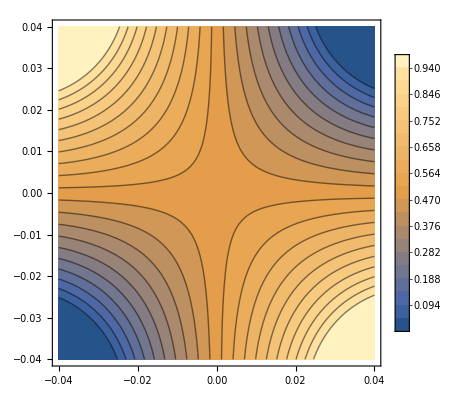

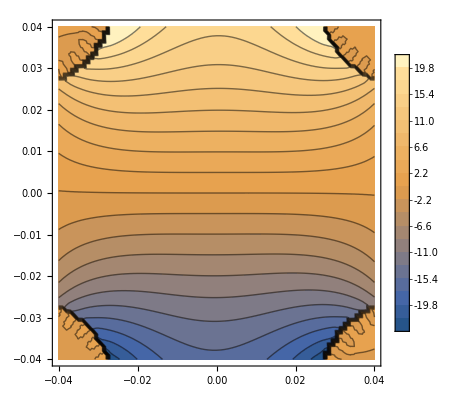

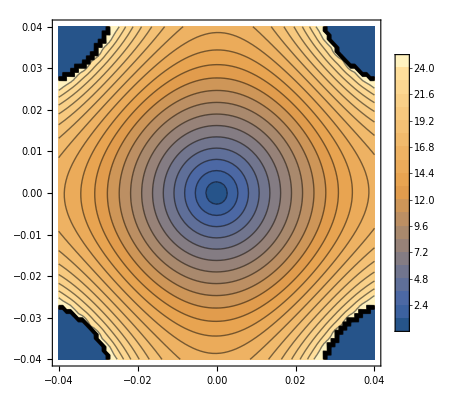

```mathematica
{pot,fx,fy,fz}={0,1,0,1,0,0}.pb;
ListContourPlot[Flatten/@({grid,pot}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({grid,fx}ᵀ),Contours->20,PlotLegends->Automatic]
ListContourPlot[Flatten/@({grid,√(fx^2+fy^2+fz^2)}ᵀ),Contours->20,PlotLegends->Automatic]
```

```mathematica
(*grid={{-0.005,0.005,10},{-0.005,0.005,10},{2.05,2.15,100}};*)
```

```mathematica
(*FitPlot[{Range[2.05,2.15,0.001],Extract[pot,Position[Flatten[EqualRange@@grid,2],{0.,0.,_}]]}ᵀ,{1,z,z^2},z]*)
```

```mathematica
grid={{0,0,0},{0,0,0},{2.05,2.15,100}};
```

```mathematica
AbsoluteTiming[pb=PotentialBasis["4rod",Sequence@@grid];]
```

{0.0524698,Null}

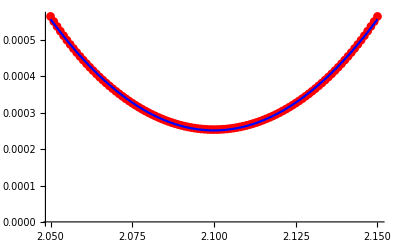

0.539689-0.51375 z+0.122321 z^2

```mathematica
{pot,fx,fy,fz}={1,0,0,0,0,1}.pb;
FitPlot[{Range[2.05,2.15,0.001],pot}ᵀ,{1,z,z^2},z]
```

```mathematica
%/.z->z+2.1//Expand
```

0.000251722-9.92887×10^-10 z+0.122321 z^2

## surface

```mathematica
ImportModelSTL@"surface"
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
cb=ChargeBasis["surface"];
```

```mathematica
range={{0,0.1,1},{-0.01,0.01,20},{0.07,0.09,20}};
```

```mathematica
pb=PotentialBasis["surface",Sequence@@range];
```

```mathematica
voltages=-500 UnitVector[12,2];
```

```mathematica
pot=(voltages.pb)⟦1⟧;
```

```mathematica
ClearAll[PotFunc];
PotFunc[x_?NumberQ,y_?NumberQ,z_?NumberQ]:=EqualRangeInterpolation[{x,y,z},Sequence@@range][pot];
```

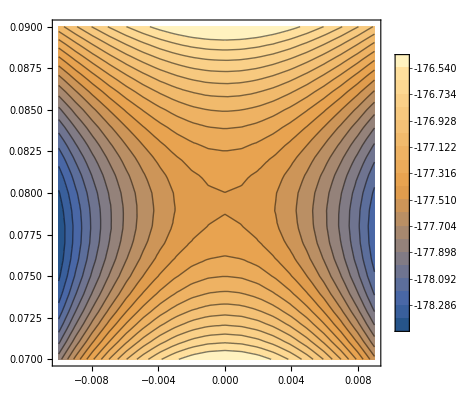

```mathematica
ContourPlot[PotFunc[0,y,z],{y,-0.01,0.009},{z,0.07,0.09},PlotLegends->Automatic,Contours->20]
```